```mathematica
ClearAll["Global`*"]
```

```mathematica
v={s,i};
rhs={(b-d)*s[t]+(b+γ)*i[t]-β*s[t]*i[t],β*s[t]*i[t]-d*(1+δ)*i[t]-γ*i[t]};
eqs=Thread[D[Through[v[t]],t]==rhs];
```

```mathematica
eqb=Solve[Thread[rhs==0],Through[v[t]]]
Jac=Outer[D,rhs,Through[v[t]]]
MatrixForm/@Simplify[Jac/.eqb]
M=Simplify[Jac/.eqb]⟦2⟧
Eigenvalues[M]//FullSimplify
```

{{s[t]→0,i[t]→0},{s[t]→(d+γ+d δ)/β,i[t]→-((b-d) (d+γ+d δ))/(β (b-d-d δ))}}

{{b-d-β i[t],b+γ-β s[t]},{β i[t],-γ-d (1+δ)+β s[t]}}

{(b-d | b+γ
0 | -γ-d (1+δ)),(((b-d) (b+γ))/(b-d (1+δ)) | b-d (1+δ)
-((b-d) (d+γ+d δ))/(b-d (1+δ)) | 0)}

{{((b-d) (b+γ))/(b-d (1+δ)),b-d (1+δ)},{-((b-d) (d+γ+d δ))/(b-d (1+δ)),0}}

{((b-d) (b+γ)-√(b-d) √((b-d) (-b+2 d+γ)^2-4 (b-d) d (b-3 d-2 γ) δ-4 d^2 (-2 b+3 d+γ) δ^2-4 d^3 δ^3))/(2 (b-d (1+δ))),((b-d) (b+γ)+√(b-d) √((b-d) (-b+2 d+γ)^2-4 (b-d) d (b-3 d-2 γ) δ-4 d^2 (-2 b+3 d+γ) δ^2-4 d^3 δ^3))/(2 (b-d (1+δ)))}

```mathematica
ic={s[0]==2.1,i[0]==1};
pars={b->0.01,d->0.0095,γ->1,δ->1,β->0.5};
tmax=2500;
sol=NDSolve[Join[eqs,ic]/.pars,v,{t,0,tmax}]
```

{{s→InterpolatingFunction[…],i→InterpolatingFunction[…]}}

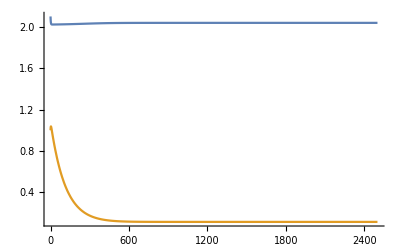

```mathematica
Plot[Evaluate[Through[v[t]]/.sol],{t,0,tmax},PlotRange->{0,All}]
```

```mathematica
Through[v[t]]/.sol/.t->tmax
```

{{2.038,0.113222}}

```mathematica
M/.pars//Eigenvalues
```

{-0.0447173,-0.0113938}

```mathematica
rhs/.pars/.{s[t]->2.1,i[t]->1}
```

{-0.03895,0.031}